# Increase precentage and Cumulative increase precentage

```mathematica
f[n_]:=n/100(*1/100{2.4,3.2,5.1,6,2,3,4,5,3,1,2,1}[[n]]*)
g[n_]:=Sum[f[i],{i,1,n}]
gg[n_]:=Exp[Sum[Log[1+f[i]],{i,1,n}]]-1
```

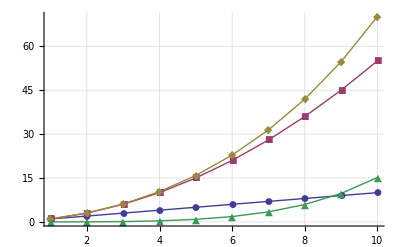

```mathematica
ListPlot[{Table[f[i]100,{i,1,10}],Table[g[i]100,{i,1,10}],Table[gg[i]100,{i,1,10}],Table[gg[i]100,{i,1,10}]-Table[g[i]100,{i,1,10}]},PlotRange->All,Joined->True,GridLines->Automatic,PlotMarkers->Automatic]
```